```mathematica
Integrate[u^(β-1)/(1+u)^(α+β),{u,0,∞}]
```

ConditionalExpression[(Gamma[α] Gamma[β])/Gamma[α+β], Re[α]>0&&Re[β]>0]

```mathematica
Integrate[Abs[Sin[θ]]^(α-1),{θ,0,2π},Assumptions->{α>0,θf>0}]
```

(2 √π Gamma[α/2])/Gamma[(1+α)/2]

```mathematica
FullSimplify[Gamma[(1+α)/2]/(√2 Gamma[α/2])((2 √π Gamma[α/2])/Gamma[(1+α)/2])/(2π)]
```

1/(√(2 π))

```mathematica
Gamma[(1+α)/2]/(√2 Gamma[α/2])Integrate[E^(-z^2/2)Abs[z]^(α-1),{z,-∞,∞},Assumptions->{α>0}]
```

2^(-1/2+α/2) Gamma[(1+α)/2]

```mathematica
Clear[H,G,F,n];

H[α_?NumericQ,u_?NumericQ]:=Module[{nmax},nmax=Max[0,Ceiling[(Sqrt[70 u]-α-1)/2]+2];
1-2^((α+3)/2)/(Sqrt[Pi] u^((α+1)/2))*Sum[Pochhammer[α+1,n]/n!*Exp[-(2 n+α+1)^2/(2 u)]*HermiteH[α,(2 n+α+1)/Sqrt[2 u]],{n,0,3nmax}]];

G[α_?NumericQ,x_?NumericQ]:=Module[{nmax},nmax=Max[1,Ceiling[Sqrt[20 x]]];
1+2 Sum[Pochhammer[(1-α)/2,n]/Pochhammer[(1+α)/2,n]*Exp[-2 n^2/x],{n,1,3nmax}]];

F[α_?NumericQ,x_?NumericQ]:=(α Sqrt[Pi])/(2^(1+α/2) Gamma[(1+α)/2])*NIntegrate[u^(α/2-1) H[α,u] G[α,u x],{u,0,10},Method->{"GlobalAdaptive","SymbolicProcessing"->0}]
```

```mathematica
F[1/2,3.2]
```

1.02587

```mathematica
α=1/2;
tablex=Table[{10^x,F[α,10^x]},{x,-2,2,0.2}]
```

{{0.01,1.},{0.0158489,1.},{0.0251189,1.},{0.0398107,1.},{0.0630957,1.},{0.1,1.},{0.158489,1.},{0.251189,1.},{0.398107,1.00005},{0.630957,1.0004},{1.,1.00189},{1.58489,1.00646},{2.51189,1.01696},{3.98107,1.03634},{6.30957,1.06691},{10.,1.11019},{15.8489,1.1673},{25.1189,1.23932},{39.8107,1.32737},{63.0957,1.43276},{100.,1.55696}}

```mathematica
Table[tablex[[i]][[2]],{i,1,Length[tablex]}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.00005,1.0004,1.00189,1.00646,1.01696,1.03634,1.06691,1.11019,1.1673,1.23932,1.32737,1.43276,1.55696}

```mathematica
{0.01,0.01778279410038923,0.03162277660168379,0.05623413251903491,0.1,0.1778279410038923,0.31622776601683794,0.5623413251903491,1.,1.7782794100389228,3.1622776601683795,5.623413251903491,10.,17.78279410038923,31.622776601683793,56.23413251903491,100.,177.82794100389228,316.22776601683796,562.341325190349,1000.}
```

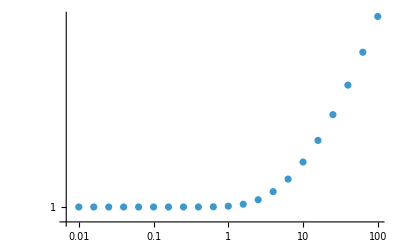

```mathematica
ListLogLogPlot[tablex]
```

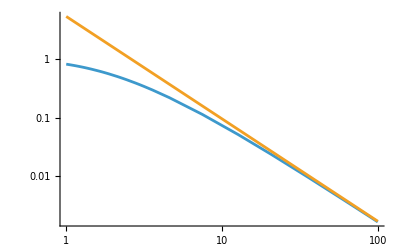

```mathematica
α=4.5;
LogLogPlot[{G[α,x],(2/x)^((α-1)/2)Gamma[(1+α)/2]},{x,1,100},PlotPoints->10,MaxRecursion->4]
Clear[α]
```

```mathematica
FullSimplify[(√π 2^(-α-1/2)α β Beta[α,β]/Gamma[(1+α)/2]^2)/(β Beta[α,β]/(√(2^(α-1))Gamma[(1+α)/2])),{α>0,β>0}]
```

(2^(-1-α/2) √π α)/Gamma[(1+α)/2]

```mathematica
α=3;
InverseLaplaceTransform[(Sin[z/(√u)]^2)^((α-1)/2)u^(α/2-1),u,s,Assumptions->{z>0,α>0}]
Clear[α]
```

1/(12 √π s^(3/2))(-3+3 HypergeometricPFQ[{},{-1/2,1/2},-s z^2]+8 ⅈ √π s^(3/2) z^3 HypergeometricPFQ[{},{2,5/2},-s z^2])

```mathematica
α=E
NIntegrate[1/x^2(1-(x/Sinh[x])^(α+1)),{x,0,∞}]
```

ⅇ

1.37748